# Komunalni odpadki občin v Sloveniji

## Med leti 2012 in 2020

## Zbiranje podatkov

Podatke sem pridobila na spletni strani https://pxweb.stat.si/SiStatData/pxweb/sl/Data/Data/2700020S.px/. Podatke sem s pomočjo programa Excel uredila in iz tabele odstranila vse nepotrebne informacije. Spodaj je uvožena urejena tabela podatkov, ki predstavlaja vse nastale in odložene komunalne odpadke od leta 2012 do 2020 za vsako občino v Sloveniji. Podatki so izraženi v enoti kilogram/prebivalca. 

Iz tabele je odstranjena vrstica 2016 (odloženi komunalni odpadki), saj za to leto tej podatki niso bili zabeleženi. Druga izjema je občina Ankaran; informacije o komunalnih odpadkih te občine so beležene komaj po letu 2015, saj je občina nastala leta 2011 in podatki, nekaj let po njenem nastanku prav tako niso zbrani in zabeleženi.

```mathematica
Podatki = Import["/Users/anesa/Desktop/prava.xlsx", "Dataset", "Headerlines" -> 1][[1]]
```

```mathematica
data = Import[NotebookDirectory[]<> "2700020S_20220827-160128.csv","Table", FieldSeparators -> ",", HeaderLines -> 3, CharacterEncoding->"WindowsEastEurope"]//Prepend[#,{"Občine", "Nastali komunalni odpadki - 2012", "Odloženi komunalni odpadki - 2012",  "Nastali komunalni odpadki - 2013", "Odloženi komunalni odpadki - 2013", "Nastali komunalni odpadki - 2014", "Odloženi komunalni odpadki - 2014", "Nastali komunalni odpadki - 2015", "Odloženi komunalni odpadki - 2015", "Nastali komunalni odpadki - 2016", "Odloženi komunalni odpadki - 2016", "Nastali komunalni odpadki - 2017", "Odloženi komunalni odpadki - 2017", "Nastali komunalni odpadki - 2018", "Odloženi komunalni odpadki - 2018", "Nastali komunalni odpadki - 2019", "Odloženi komunalni odpadki - 2019", "Nastali komunalni odpadki - 2020", "Odloženi komunalni odpadki - 2020"} ]& //ResourceFunction["DatasetWithHeaders"] ;
data [Drop[Range[213], {3}],Drop[Range[19],{11}] ]//Query[All, <|#,"skupaj" -> Total[Drop[#,{1}]]|>&]
(*Izpusti 11 stolpec (leto 2016) in 3 vrstico (Ankaran)*)
```

## Število odpadkov v Sloveniji

```mathematica
(*NastaliodpadkiSLO =Transpose[data[[{1,215},{1,2,4,6,8,10,11,13,15,17}]]]*)
NastaliodpadkiSLO = data[1,{1,2,4,6,8,10,12,14,16,18}]
```

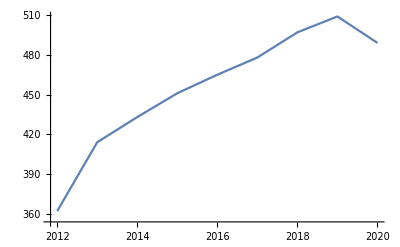

```mathematica
ListLinePlot[{{2012,362},{2013,414},{2014,433},{2015,451},{2016,465},{2017,478},{2018,497},{2019,509},{2020,489}}]
```

Število nastalih odpadkov v Sloveniji se iz leta v leto povečuje. Številke so nam pokazale, da kljub osveščenosti o globalnem segrevanju in drugih naravnih problemih ljudje neustavljivo uničujemo naš planet. Ustavi nas lahko samo mati narava, kot je iz krivulje razvidno po letu 2019. Po skoraj desetletju je naklon premice o količini nastalih odpadkov prvič negativen. Po pojavitvi prve različice nalezljive bolezni Covid-19 in prvih ukrepih o zmanjšanju druženja in zadrževanju doma,  se je po različnih raziskavah bistveno zmanjšala količina odpadkov v proizvodnji dejavnosti, nekoliko povečala pa količina odpadkov v gospodinjstvih. Ni se zmanjšala samo količina odpadkov temveč je bolezen vse dejavnike onesnaževanja potisnila v kot.

```mathematica
OdloženiodpadkiSLO =Transpose[Podatki[[{1,215},{1,3,5,7,9,12,14,16,18}]]]
```

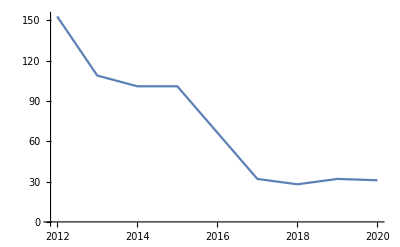

```mathematica
ListLinePlot[{{2012,153},{2013,109},{2014,101},{2015,101},{2017,32},{2018,28},{2019,32},{2020,31}}]
```

Krivulja o odloženih odpadkih pa nakazuje na nekoliko bolj svetla in zelena leta za naš planet in sicer se je količina odloženih odpadkov bistveno zmanjšala po sprejeti odredbi o odlaganju odpadkov po letu 2006. Bistveno se je povečala količina ločeno zbranih odpadkov, stem tudi količina recikliranih in predelanih odpadkov, povečal se je tudi izvoz odpadkov, ki je nekoliko večji od uvoza. Po sprejetih odlokih so ljudje začeli bistveno bolj ločevati in stem narediti minimalen korak k bolšemu svetu. Pri večjem osveščanju in uvajanju različnih drugih ukrepov in zakonov bi lahko prisilili človeško ignoranco in lenobo h koncu in skupaj ustavarjali zelen planet.

## 10 Najbolj onesnaženih občin

```mathematica
Nasaliodpadkinajonesnazenih =Transpose[Podatki[[{1,9,19,63,70,71,76,85,116,123,134},{1,2,4,6,8,10,11,13,15,17,19}]]]
```

Podatke o prvih 10 najbolj onesnaženih občinah sem dobila tako, da sem seštela podatke o odloženih ter zbranih odpadkih za vsako občino med sabo in primerjala rezultate med seboj. Razlogi za veliko onesnaženost teh mest so različni. Za nekatere je velik razvita industrijska obrt ter razvito kmetijstvo. Brez dvoma pa lahko rečemo, da je najbolj problematičen dejavnik turizem, zato se na seznamu med prvimi pojavljajo Bled, Kranjska Gora, Ptuj, Ljubljana, Koper, Piran...